### Start choosing the example:

```mathematica
t=20;
beta = 1;
A =0;
g[x]
```

x

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{7,U1},{8,U2},{9,U3}},"Switching Costs"->{(*{5,6,7,1},{5,6,8,1},{5,6,9,1},{7,6,5,1},{7,6,8,1},{7,6,9,1},{8,6,5,1},{8,6,7,1},{8,6,9,1},{9,6,5,1},{9,6,7,1},{9,6,8,1}*)}|>;
d2e=Data2Equations[Data/.{I1->200,I2->200,U1->0,U2->0, U3->0}];
crit=CriticalCongestionSolver[d2e = Data2Equations[Data/.{I1->200,I2->200,U1->0,U2->0, U3->0}]];//AbsoluteTiming
```

{200-u1+u4==0&&200-u25+u4==0&&400-u4+u6==0&&400-u6+u8==0&&400+u13-u8==0&&jt15+u12-u13==0&&jt16-u13+u14==0&&400-jt15-jt16-u13+u16==0,jt15≥0&&jt16≥0&&-1000≤u12≤0&&-1000≤u14≤0&&-1000≤u16≤0&&jt15+jt16≤400,(jt15==0||u12==0)&&(jt16==0||u14==0)&&(jt15+jt16==400||u16==0)}

{0.073272,Null}

```mathematica
NS=And@@{200-u1+u4==0&&200-u25+u4==0&&400-u4+u6==0&&400-u6+u8==0&&400+u13-u8==0&&jt15+u12-u13==0&&jt16-u13+u14==0&&400-jt15-jt16-u13+u16==0,jt15≥0&&jt16≥0&&-1000≤u12≤0&&-1000≤u14≤0&&-1000≤u16≤0&&jt15+jt16≤400,(jt15==0||u12==0)&&(jt16==0||u14==0)&&(jt15+jt16==400||u16==0)};
Reduce[NS,Reals]//AbsoluteTiming
```

{0.025542,u8==1600/3&&u16==0&&u14==0&&u6==2800/3&&u4==400+u6&&u25==200+u4&&u13==400/3&&u12==-400+3 u13&&u1==200+u4&&jt16==u13&&jt15==-u12+u13}

```mathematica
crit=CriticalCongestionSolver[d2e = Data2Equations[Data/.{I1->1,I2->2,U1->1,U2->2, U3->3}]];//AbsoluteTiming
```

Switching costs are consistent

Part::partw: Part 3 of #1 does not exist.

Part::pkspec1: The expression #1 cannot be used as a part specification.

NewReduce...{jt15≥0&&jt16≥0&&u1≤1400+jt15&&400+jt15≤u1&&u1≤1400+jt16&&400+jt16≤u1&&800≤jt15+jt16+u1≤1800&&jt15+jt16≤400,3⟦#1⟧}

BooleanConvert...jt15≥0&&jt16≥0&&u1≤1400+jt15&&400+jt15≤u1&&u1≤1400+jt16&&400+jt16≤u1&&800≤jt15+jt16+u1≤1800&&jt15+jt16≤400&&3⟦#1⟧

Part::pkspec1: The expression #1 cannot be used as a part specification.

NewReduce...{800≤jt15+jt16+u1≤1800&&jt15≥0&&jt16≥0&&400+jt15≤u1&&400+jt16≤u1&&jt15+jt16≤400&&u1≤1400+jt15&&u1≤1400+jt16&&3⟦#1⟧,3⟦#1⟧}

BooleanConvert...800≤jt15+jt16+u1≤1800&&jt15≥0&&jt16≥0&&400+jt15≤u1&&400+jt16≤u1&&jt15+jt16≤400&&u1≤1400+jt15&&u1≤1400+jt16&&3⟦#1⟧

33: {{True,800≤jt15+jt16+u1≤1800&&jt15≥0&&jt16≥0&&400+jt15≤u1&&400+jt16≤u1&&jt15+jt16≤400&&u1≤1400+jt15&&u1≤1400+jt16&&3⟦#1⟧,True},<|j24→200,j26→200,j23→0,j25→0,j17→0,j19→0,j21→0,j2→200,j4→200,j1→0,j3→0,j6→400,j5→0,j8→400,j7→0,j10→400,j9→0,j12→jt15,j14→jt16,j16→400-jt15-jt16,j11→0,j18→jt15,j13→0,j20→jt16,j15→0,j22→400-jt15-jt16,u18→0,u20→0,u22→0,jt11→400,jt12→0,jt17→400-jt15-jt16,jt2→200,jt20→0,jt21→0,jt23→0,jt26→0,jt27→jt15,jt28→0,jt29→jt16,jt3→0,jt30→0,jt31→400-jt15-jt16,jt32→0,jt4→200,jt5→0,jt6→200,jt7→0,jt8→200,jt9→0,u17→0,u19→0,u21→0,u24→u1,u26→u1,jt1→0,jt10→0,jt13→400,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u10→-1400+u1,u11→-1400+u1,u15→-1400+u1,u2→-200+u1,u23→u1,u3→u1,u5→-200+u1,u7→-600+u1,u9→-1000+u1,u12→-1400-jt15+u1,u13→-1400+u1,u14→-1400-jt16+u1,u16→-1800+jt15+jt16+u1,u25→u1,u4→-200+u1,u6→-600+u1,u8→-1000+u1|>}

Reduce::naqs: 800≤jt15+jt16+u1≤1800&&jt15≥0&&jt16≥0&&400+jt15≤u1&&400+jt16≤u1&&jt15+jt16≤400&&u1≤1400+jt15&&u1≤1400+jt16&&3⟦#1⟧ is not a quantified system of equations and inequalities.

Part::pkspec1: The expression #1 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NewReduce...{Reduce[800≤jt15+jt16+u1≤1800&&jt15≥0&&jt16≥0&&400+jt15≤u1&&400+jt16≤u1&&jt15+jt16≤400&&u1≤1400+jt15&&u1≤1400+jt16&&3⟦#1⟧,ℝ],3⟦#1⟧}

BooleanConvert...Reduce[800≤jt15+jt16+u1≤1800&&jt15≥0&&jt16≥0&&400+jt15≤u1&&400+jt16≤u1&&jt15+jt16≤400&&u1≤1400+jt15&&u1≤1400+jt16&&3⟦#1⟧,ℝ]

Multiple solutions: {Reduce[800≤jt15+jt16+u1≤1800&&jt15≥0&&jt16≥0&&400+jt15≤u1&&400+jt16≤u1&&jt15+jt16≤400&&u1≤1400+jt15&&u1≤1400+jt16&&3⟦#1⟧,ℝ],<|j24→200,j26→200,j23→0,j25→0,j17→0,j19→0,j21→0,j2→200,j4→200,j1→0,j3→0,j6→400,j5→0,j8→400,j7→0,j10→400,j9→0,j12→jt15,j14→jt16,j16→400-jt15-jt16,j11→0,j18→jt15,j13→0,j20→jt16,j15→0,j22→400-jt15-jt16,u18→0,u20→0,u22→0,jt11→400,jt12→0,jt17→400-jt15-jt16,jt2→200,jt20→0,jt21→0,jt23→0,jt26→0,jt27→jt15,jt28→0,jt29→jt16,jt3→0,jt30→0,jt31→400-jt15-jt16,jt32→0,jt4→200,jt5→0,jt6→200,jt7→0,jt8→200,jt9→0,u17→0,u19→0,u21→0,u24→u1,u26→u1,jt1→0,jt10→0,jt13→400,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u10→-1400+u1,u11→-1400+u1,u15→-1400+u1,u2→-200+u1,u23→u1,u3→u1,u5→-200+u1,u7→-600+u1,u9→-1000+u1,u12→-1400-jt15+u1,u13→-1400+u1,u14→-1400-jt16+u1,u16→-1800+jt15+jt16+u1,u25→u1,u4→-200+u1,u6→-600+u1,u8→-1000+u1|>}

Picking one...

FindInstance::naqs: Reduce[800≤jt15+jt16+u1≤1800&&jt15≥0&&jt16≥0&&400+jt15≤u1&&400+jt16≤u1&&jt15+jt16≤400&&u1≤1400+jt15&&u1≤1400+jt16&&3⟦#1⟧,]&&u1>0&&jt15>0&&jt16>0 is not a quantified system of equations and inequalities.

ReplaceAll::reps: {Association[First[FindInstance[NewSystem$8158&&And@@(«1»&)/@vars$8158,vars$8158,]]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceAll and Association at positions 1 and 2 are expected to be the same.

{0.398591,Null}

Switching costs are consistent

Part::pkspec1: The expression #1 cannot be used as a part specification.

NewReduce...{jt15≥0&&jt16≥0&&jt15+jt16≤3&&u1≤11+jt15&&jt15≤989+u1&&u1≤12+jt16&&jt16≤988+u1&&-984≤jt15+jt16+u1≤16,3⟦#1⟧}

BooleanConvert...jt15≥0&&jt16≥0&&jt15+jt16≤3&&u1≤11+jt15&&jt15≤989+u1&&u1≤12+jt16&&jt16≤988+u1&&-984≤jt15+jt16+u1≤16&&3⟦#1⟧

Part::pkspec1: The expression #1 cannot be used as a part specification.

NewReduce...{-984≤jt15+jt16+u1≤16&&jt15≥0&&jt16≥0&&jt15≤989+u1&&jt16≤988+u1&&jt15+jt16≤3&&u1≤11+jt15&&u1≤12+jt16&&3⟦#1⟧,3⟦#1⟧}

BooleanConvert...-984≤jt15+jt16+u1≤16&&jt15≥0&&jt16≥0&&jt15≤989+u1&&jt16≤988+u1&&jt15+jt16≤3&&u1≤11+jt15&&u1≤12+jt16&&3⟦#1⟧

33: {{True,-984≤jt15+jt16+u1≤16&&jt15≥0&&jt16≥0&&jt15≤989+u1&&jt16≤988+u1&&jt15+jt16≤3&&u1≤11+jt15&&u1≤12+jt16&&3⟦#1⟧,True},<|j24→1,j26→2,j23→0,j25→0,j17→0,j19→0,j21→0,j2→1,j4→2,j1→0,j3→0,j6→3,j5→0,j8→3,j7→0,j10→3,j9→0,j12→jt15,j14→jt16,j16→3-jt15-jt16,j11→0,j18→jt15,j13→0,j20→jt16,j15→0,j22→3-jt15-jt16,u18→1,u20→2,u22→3,jt11→3,jt12→0,jt17→3-jt15-jt16,jt2→1,jt20→0,jt21→0,jt23→0,jt26→0,jt27→jt15,jt28→0,jt29→jt16,jt3→0,jt30→0,jt31→3-jt15-jt16,jt32→0,jt4→2,jt5→0,jt6→1,jt7→0,jt8→2,jt9→0,u17→1,u19→2,u21→3,u24→u1,u26→1+u1,jt1→0,jt10→0,jt13→3,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u10→-10+u1,u11→-10+u1,u15→-10+u1,u2→-1+u1,u23→u1,u3→1+u1,u5→-1+u1,u7→-4+u1,u9→-7+u1,u12→-10-jt15+u1,u13→-10+u1,u14→-10-jt16+u1,u16→-13+jt15+jt16+u1,u25→1+u1,u4→-1+u1,u6→-4+u1,u8→-7+u1|>}

Reduce::naqs: -984≤jt15+jt16+u1≤16&&jt15≥0&&jt16≥0&&jt15≤989+u1&&jt16≤988+u1&&jt15+jt16≤3&&u1≤11+jt15&&u1≤12+jt16&&3⟦#1⟧ is not a quantified system of equations and inequalities.

Part::pkspec1: The expression #1 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NewReduce...{Reduce[-984≤jt15+jt16+u1≤16&&jt15≥0&&jt16≥0&&jt15≤989+u1&&jt16≤988+u1&&jt15+jt16≤3&&u1≤11+jt15&&u1≤12+jt16&&3⟦#1⟧,ℝ],3⟦#1⟧}

BooleanConvert...Reduce[-984≤jt15+jt16+u1≤16&&jt15≥0&&jt16≥0&&jt15≤989+u1&&jt16≤988+u1&&jt15+jt16≤3&&u1≤11+jt15&&u1≤12+jt16&&3⟦#1⟧,ℝ]

Multiple solutions: {Reduce[-984≤jt15+jt16+u1≤16&&jt15≥0&&jt16≥0&&jt15≤989+u1&&jt16≤988+u1&&jt15+jt16≤3&&u1≤11+jt15&&u1≤12+jt16&&3⟦#1⟧,ℝ],<|j24→1,j26→2,j23→0,j25→0,j17→0,j19→0,j21→0,j2→1,j4→2,j1→0,j3→0,j6→3,j5→0,j8→3,j7→0,j10→3,j9→0,j12→jt15,j14→jt16,j16→3-jt15-jt16,j11→0,j18→jt15,j13→0,j20→jt16,j15→0,j22→3-jt15-jt16,u18→1,u20→2,u22→3,jt11→3,jt12→0,jt17→3-jt15-jt16,jt2→1,jt20→0,jt21→0,jt23→0,jt26→0,jt27→jt15,jt28→0,jt29→jt16,jt3→0,jt30→0,jt31→3-jt15-jt16,jt32→0,jt4→2,jt5→0,jt6→1,jt7→0,jt8→2,jt9→0,u17→1,u19→2,u21→3,u24→u1,u26→1+u1,jt1→0,jt10→0,jt13→3,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u10→-10+u1,u11→-10+u1,u15→-10+u1,u2→-1+u1,u23→u1,u3→1+u1,u5→-1+u1,u7→-4+u1,u9→-7+u1,u12→-10-jt15+u1,u13→-10+u1,u14→-10-jt16+u1,u16→-13+jt15+jt16+u1,u25→1+u1,u4→-1+u1,u6→-4+u1,u8→-7+u1|>}

Picking one...

FindInstance::naqs: Reduce[-984≤jt15+jt16+u1≤16&&jt15≥0&&jt16≥0&&jt15≤989+u1&&jt16≤988+u1&&jt15+jt16≤3&&u1≤11+jt15&&u1≤12+jt16&&3⟦#1⟧,]&&u1>0&&jt15>0&&jt16>0 is not a quantified system of equations and inequalities.

ReplaceAll::reps: {Association[First[FindInstance[NewSystem$8287&&And@@(«1»&)/@vars$8287,vars$8287,]]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceAll and Association at positions 1 and 2 are expected to be the same.

{0.367777,Null}

```mathematica
crit
```

<|j24→1,j26→2,j23→0,j25→0,j17→0,j19→0,j21→0,j2→1,j4→2,j1→0,j3→0,j6→3,j5→0,j8→3,j7→0,j10→3,j9→0,j12→2,j14→1,j16→0,j11→0,j18→2,j13→0,j20→1,j15→0,j22→0,u18→1,u20→2,u22→3,jt11→3,jt12→0,jt17→0,jt2→1,jt20→0,jt21→0,jt23→0,jt26→0,jt27→2,jt28→0,jt29→1,jt3→0,jt30→0,jt31→0,jt32→0,jt4→2,jt5→0,jt6→1,jt7→0,jt8→2,jt9→0,u17→1,u19→2,u21→3,u24→13,u26→14,jt1→0,jt10→0,jt13→3,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u10→3,u11→3,u12→1,u14→2,u15→3,u16→3,u2→12,u23→13,u3→14,u5→12,u7→9,u9→6,jt15→2,jt16→1,u1→13,u13→3,u25→14,u4→12,u6→9,u8→6|>

```mathematica
NonLinear[d2e][crit]
```

Preprocessing done!

raw: {-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}

NIntegrate::inumr: The integrand M[1,x,1->3]^(-1+alpha) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand M[2,x,2->3]^(-1+alpha) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

with initrules: {1-NIntegrate[M[1,x,1->3]^(alpha-1),{x,0,1}],2-2 NIntegrate[M[2,x,2->3]^(alpha-1),{x,0,1}],3-3 NIntegrate[M[3,x,3->4]^(alpha-1),{x,0,1}],3-3 NIntegrate[M[3,x,4->5]^(alpha-1),{x,0,1}],3-3 NIntegrate[M[3,x,5->6]^(alpha-1),{x,0,1}],jt15-IntM[jt15,6->7],jt16-IntM[jt16,6->8],3-jt15-jt16-IntM[3-jt15-jt16,6->9]}

with j: {1-NIntegrate[M[1,x,1->3]^(alpha-1),{x,0,1}],2-2 NIntegrate[M[2,x,2->3]^(alpha-1),{x,0,1}],3-3 NIntegrate[M[3,x,3->4]^(alpha-1),{x,0,1}],3-3 NIntegrate[M[3,x,4->5]^(alpha-1),{x,0,1}],3-3 NIntegrate[M[3,x,5->6]^(alpha-1),{x,0,1}],2-2 NIntegrate[M[2,x,6->7]^(alpha-1),{x,0,1}],1-NIntegrate[M[1,x,6->8]^(alpha-1),{x,0,1}],0.}

-j1+j2-u1+u2==-j1+j2-IntM[-j1+j2,1->3]&&-j3+j4-u3+u4==-j3+j4-IntM[-j3+j4,2->3]&&-j5+j6-u5+u6==-j5+j6-IntM[-j5+j6,3->4]&&-j7+j8-u7+u8==-j7+j8-IntM[-j7+j8,4->5]&&j10-j9+u10-u9==j10-j9-IntM[j10-j9,5->6]&&-j11+j12-u11+u12==-j11+j12-IntM[-j11+j12,6->7]&&-j13+j14-u13+u14==-j13+j14-IntM[-j13+j14,6->8]&&-j15+j16-u15+u16==-j15+j16-IntM[-j15+j16,6->9]

-j1+j2-u1+u2==1-NIntegrate[M[1,x,1->3]^(alpha-1),{x,0,1}]&&-j3+j4-u3+u4==2-2 NIntegrate[M[2,x,2->3]^(alpha-1),{x,0,1}]&&-j5+j6-u5+u6==3-3 NIntegrate[M[3,x,3->4]^(alpha-1),{x,0,1}]&&-j7+j8-u7+u8==3-3 NIntegrate[M[3,x,4->5]^(alpha-1),{x,0,1}]&&j10-j9+u10-u9==3-3 NIntegrate[M[3,x,5->6]^(alpha-1),{x,0,1}]&&-j11+j12-u11+u12==2-2 NIntegrate[M[2,x,6->7]^(alpha-1),{x,0,1}]&&-j13+j14-u13+u14==1-NIntegrate[M[1,x,6->8]^(alpha-1),{x,0,1}]&&-j15+j16-u15+u16==0.

<|j24→1,j26→2,j23→0,j25→0,j17→0,j19→0,j21→0,j2→1,j4→2,j1→0,j3→0,j6→3,j5→0,j8→3,j7→0,j10→3,j9→0,j12→jt15,j14→jt16,j16→3-jt15-jt16,j11→0,j18→jt15,j13→0,j20→jt16,j15→0,j22→3-jt15-jt16,u18→1,u20→2,u22→3,jt11→3,jt12→0,jt17→3-jt15-jt16,jt2→1,jt20→0,jt21→0,jt23→0,jt26→0,jt27→jt15,jt28→0,jt29→jt16,jt3→0,jt30→0,jt31→3-jt15-jt16,jt32→0,jt4→2,jt5→0,jt6→1,jt7→0,jt8→2,jt9→0,u17→1,u19→2,u21→3,u24→u1,u26→u25,jt1→0,jt10→0,jt13→3,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u10→6.-1. jt15-1. jt16,u11→6.-1. jt15-1. jt16,u12→1,u14→2,u15→6.-1. jt15-1. jt16,u16→3,u2→u4,u23→u1,u3→u25,u5→u4,u7→u6,u9→u8,u13→6.-1. jt15-1. jt16,NIntegrate[M[1,x,1->3]^(alpha-1),{x,0,1}]→0.+1. u1-1. u4,NIntegrate[M[1,x,6->8]^(alpha-1),{x,0,1}]→5.-1. jt15-2. jt16,NIntegrate[M[2,x,2->3]^(alpha-1),{x,0,1}]→0.+0.5 u25-0.5 u4,NIntegrate[M[2,x,6->7]^(alpha-1),{x,0,1}]→3.5-1. jt15-0.5 jt16,NIntegrate[M[3,x,3->4]^(alpha-1),{x,0,1}]→0.+0.333333 u4-0.333333 u6,NIntegrate[M[3,x,4->5]^(alpha-1),{x,0,1}]→0.+0.333333 u6-0.333333 u8,NIntegrate[M[3,x,5->6]^(alpha-1),{x,0,1}]→-2.+0.333333 jt15+0.333333 jt16+0.333333 u8|>

```mathematica
IntM
```

```mathematica
crit
```

<|j24→200,j26→200,j23→0,j25→0,j17→0,j19→0,j21→0,j2→200,j4→200,j1→0,j3→0,j6→400,j5→0,j8→400,j7→0,j10→400,j9→0,j12→400/3,j14→400/3,j16→400/3,j11→0,j18→400/3,j13→0,j20→400/3,j15→0,j22→400/3,u18→0,u20→0,u22→0,jt11→400,jt12→0,jt17→400/3,jt2→200,jt20→0,jt21→0,jt23→0,jt26→0,jt27→400/3,jt28→0,jt29→400/3,jt3→0,jt30→0,jt31→400/3,jt32→0,jt4→200,jt5→0,jt6→200,jt7→0,jt8→200,jt9→0,u17→0,u19→0,u21→0,u24→4600/3,u26→4600/3,jt1→0,jt10→0,jt13→400,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u10→400/3,u11→400/3,u12→0,u14→0,u15→400/3,u16→0,u2→4000/3,u23→4600/3,u3→4600/3,u5→4000/3,u7→2800/3,u9→1600/3,jt15→400/3,jt16→400/3,u1→4600/3,u13→400/3,u25→4600/3,u4→4000/3,u6→2800/3,u8→1600/3|>

```mathematica
in = u1==u23&&u25==u3&&u2==u4&&u2==u5&&u4==u5&&u6==u7&&u8==u9&&u12==1&&u14==2&&u16==3&&jt1≥0&&3+jt14≥jt1+jt13&&3+jt14≥jt1+jt10+jt13&&jt1+jt10+jt13≥2+jt14&&jt1+jt10≥jt14&&2+jt14≥jt1+jt10&&jt14≥jt10&&jt10≥0&&jt13≥0&&jt14≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt13≥jt15+jt16&&jt18≥0&&jt19≥0&&jt18+jt19≤0&&jt14≥jt18+jt24&&jt22≥0&&jt18+jt24≥jt14+jt22&&jt24≥0&&jt25≥0&&jt24+jt25≤0&&jt15+jt22+jt25≥0&&jt16+jt19≥jt24+jt25&&jt13+jt24≥jt14+jt15+jt16+jt19+jt22&&jt1≥0&&3+jt14≥jt1+jt13&&jt14≥0&&jt13≥0&&jt14≥0&&jt13≥0&&jt14≥0&&jt13≥0&&jt15+jt22+jt25≥0&&jt16+jt19≥jt24+jt25&&jt13+jt24≥jt14+jt15+jt16+jt19+jt22&&jt15+jt22+jt25≥0&&jt16+jt19≥jt24+jt25&&jt13+jt24≥jt14+jt15+jt16+jt19+jt22&&jt1≥0&&3+jt14≥jt1+jt13&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&jt1==0&&jt1+jt13==3+jt14&&(jt14==0||jt13==0)&&(jt14==0||jt13==0)&&(jt14==0||jt13==0)&&jt1==0&&jt1+jt13==3+jt14&&jt1==0&&(jt10==0||jt1+jt10==2+jt14)&&(jt13==0||jt14==0)&&(jt13==0||jt14==0)&&(jt15==0||jt18==0)&&(jt16==0||jt14==jt18+jt24)&&(jt13==jt15+jt16||jt24==0)&&(jt19==0||jt22==0)&&(jt18+jt19==0||jt25==0)&&(jt14+jt22==jt18+jt24||jt24+jt25==0)&&jt1+jt13==3+jt14&&(jt1+jt10+jt13==3+jt14||jt1+jt10==jt14)&&(jt1+jt10+jt13==2+jt14||jt10==jt14)&&(jt1==0||u1==u23)&&u1==u23&&(jt1+jt13==3+jt14||u25==u3)&&u25==u3&&(jt1+jt10+jt13==3+jt14||u2==u4)&&(jt1+jt10+jt13==2+jt14||u2==u5)&&(jt1+jt10==jt14||u2==u4)&&(jt1+jt10==2+jt14||u4==u5)&&(jt10==jt14||u2==u5)&&(jt10==0||u4==u5)&&(jt13==0||u6==u7)&&(jt14==0||u6==u7)&&(jt13==0||u8==u9)&&(jt14==0||u8==u9)&&(jt15==0||u10==1+u11)&&(jt16==0||u10==1+u13)&&(jt13==jt15+jt16||u10==1+u15)&&(jt18==0||1+u10==u11)&&(jt19==0||u11==1+u13)&&(jt18+jt19==0||u11==1+u15)&&(jt14==jt18+jt24||1+u10==u13)&&(jt22==0||1+u11==u13)&&(jt14+jt22==jt18+jt24||u13==1+u15)&&(jt24==0||1+u10==u15)&&(jt25==0||1+u11==u15)&&(jt24+jt25==0||1+u13==u15)&&(jt15+jt22+jt25==0||u12==1)&&(jt16+jt19==jt24+jt25||u14==2)&&(jt13+jt24==jt14+jt15+jt16+jt19+jt22||u16==3)&&j24==1&&j26==2&&j23==jt1&&j25+jt1+jt13==3+jt14&&j17==0&&j19==0&&j21==0&&j2==1&&j4==2&&j1==jt1&&j3+jt1+jt13==3+jt14&&j6==jt13&&j5==jt14&&j8==jt13&&j7==jt14&&j10==jt13&&j9==jt14&&j12==jt15+jt22+jt25&&j14+jt24+jt25==jt16+jt19&&j16+jt14+jt15+jt16+jt19+jt22==jt13+jt24&&j11==0&&j18==jt15+jt22+jt25&&j13==0&&j20+jt24+jt25==jt16+jt19&&j15==0&&j22+jt14+jt15+jt16+jt19+jt22==jt13+jt24&&u18==1&&u20==2&&u22==3&&jt11==jt13&&jt12==jt14&&jt13==jt15+jt16+jt17&&jt2==1&&jt18+jt19+jt20==0&&jt14==jt18+jt21+jt24&&jt14+jt22+jt23==jt18+jt24&&jt24+jt25+jt26==0&&jt15+jt22+jt25==jt27&&jt28==0&&jt16+jt19==jt24+jt25+jt29&&jt1+jt13+jt3==3+jt14&&jt30==0&&jt13+jt24==jt14+jt15+jt16+jt19+jt22+jt31&&jt32==0&&jt4==2&&jt1+jt10+jt13+jt5==3+jt14&&jt1+jt10+jt13==2+jt14+jt6&&jt1+jt10==jt14+jt7&&jt1+jt10+jt8==2+jt14&&jt10+jt9==jt14&&u17==1&&u19==2&&u21==3&&u23==u24&&u25==u26;
out=jt15≥0&&jt16≥0&&jt15+jt16≤3&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&(jt15==0||u10==1+u11)&&(jt16==0||u10==1+u13)&&(jt15+jt16==3||u10==1+u15)&&j24==1&&j26==2&&j23==0&&j25==0&&j17==0&&j19==0&&j21==0&&j2==1&&j4==2&&j1==0&&j3==0&&j6==3&&j5==0&&j8==3&&j7==0&&j10==3&&j9==0&&j12==jt15&&j14==jt16&&j16+jt15+jt16==3&&j11==0&&j18==jt15&&j13==0&&j20==jt16&&j15==0&&j22+jt15+jt16==3&&u18==1&&u20==2&&u22==3&&jt11==3&&jt12==0&&jt15+jt16+jt17==3&&jt2==1&&jt20==0&&jt21==0&&jt23==0&&jt26==0&&jt15==jt27&&jt28==0&&jt16==jt29&&jt3==0&&jt30==0&&jt15+jt16+jt31==3&&jt32==0&&jt4==2&&jt5==0&&jt6==1&&jt7==0&&jt8==2&&jt9==0&&u17==1&&u19==2&&u21==3&&u1==u24&&u25==u26&&jt1==0&&jt10==0&&jt13==3&&jt14==0&&jt18==0&&jt19==0&&jt22==0&&jt24==0&&jt25==0&&u12==1&&u14==2&&u16==3&&u2==u4&&u1==u23&&u25==u3&&u4==u5&&u6==u7&&u8==u9;
int=Intersection[in,out];
Reduce[Equivalent[Select[in, Not[MemberQ[int,#]]&],
Select[out, Not[MemberQ[int,#]]&]],Reals]//AbsoluteTiming
Reduce[Equivalent[in,out],Reals]//AbsoluteTiming
```

$Aborted

```mathematica
in=jt15≥0&&jt16≥0&&jt15+jt16≤201&&jt15≥0&&jt16≥0&&jt15+jt16≤201&&jt15≥0&&jt16≥0&&jt15+jt16≤201&&jt15≥0&&jt16≥0&&jt15+jt16≤201&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&(jt15==0||u10==1+u11)&&(jt16==0||u10==1+u13)&&(jt15+jt16==201||u10==1+u15);
out=jt15≥0&&jt16≥0&&jt15+jt16≤201&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&(jt15==0||u10==1+u11)&&(jt16==0||u10==1+u13)&&(jt15+jt16==201||u10==1+u15);
int=Intersection[in,out]
Reduce[Implies[Select[in, Not[MemberQ[int,#]]&],
Select[out, Not[MemberQ[int,#]]&]],Reals]//AbsoluteTiming
Reduce[Equivalent[Select[in, Not[MemberQ[int,#]]&],
Select[out, Not[MemberQ[int,#]]&]],Reals]//AbsoluteTiming
Reduce[Equivalent[in,out],Reals]//AbsoluteTiming
```

jt15≥0&&jt16≥0&&jt15+jt16≤201&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&(jt15==0||u10==1+u11)&&(jt16==0||u10==1+u13)&&(jt15+jt16==201||u10==1+u15)

{0.000183,True}

{0.000106,True}

{0.000839,True}

```mathematica
MFGEquations=D2E[Data/.{I1->1,I2->2,U1->1,U2->2, U3->3}];//Timing
```

{0.257057,Null}

```mathematica
jj=d2e["js"];
```

```mathematica
MFGEquations["RulesCriticalCase"]
```

<|j2→1,j23→0,j4→2,j25→0,j1→0,j3→0,j6→jt13,j5→-3+jt13,j8→jt13,j7→-3+jt13,j10→jt13,j9→-3+jt13,j12→jt15-jt21-jt23+jt25,j14→3-jt15-jt17-jt20+jt21-jt25,j16→jt17+jt20+jt23,j11→0,j18→jt15-jt21-jt23+jt25,j13→0,j20→3-jt15-jt17-jt20+jt21-jt25,j15→0,j22→jt17+jt20+jt23,j24→1,j26→2,u18→1,u20→2,u22→3,u4→-1+u1,u5→-1+u1,u7→-4+u1,u9→-7+u1,u11→-10+u1,u13→-10+u1,u15→-10+u1,jt1→0,jt28→0,jt3→0,jt30→0,jt32→0,u17→1,u19→2,u21→3,u24→u23,u26→u25,j17→0,j19→0,j21→0,jt10→-1+jt6,jt11→jt13,jt12→-3+jt13,jt14→-3+jt13,jt16→jt13-jt15-jt17,jt19→-jt18-jt20,jt2→1,jt22→-jt21-jt23,jt24→-3+jt13-jt18-jt21,jt26→3-jt13+jt18+jt21-jt25,jt27→jt15-jt21-jt23+jt25,jt29→3-jt15-jt17-jt20+jt21-jt25,jt31→jt17+jt20+jt23,jt4→2,jt5→1-jt6,jt7→2-jt13+jt6,jt8→jt13-jt6,jt9→-2+jt13-jt6,u10→-10+u1,u12→-10-jt15+jt21+jt23-jt25+u1,u14→-13+jt15+jt17+jt20-jt21+jt25+u1,u16→-10-jt17-jt20-jt23+u1,u2→-1+u1,u3→1+u1,u6→-4+u1,u8→-7+u1|>

```mathematica
jj/.<|j2->1,j23->0,j4->2,j25->0,j1->0,j3->0,j6->jt13,j5->-3+jt13,j8->jt13,j7->-3+jt13,j10->jt13,j9->-3+jt13,j12->jt15-jt21-jt23+jt25,j14->3-jt15-jt17-jt20+jt21-jt25,j16->jt17+jt20+jt23,j11->0,j18->jt15-jt21-jt23+jt25,j13->0,j20->3-jt15-jt17-jt20+jt21-jt25,j15->0,j22->jt17+jt20+jt23,j24->1,j26->2,u18->1,u20->2,u22->3,u4->-1+u1,u5->-1+u1,u7->-4+u1,u9->-7+u1,u11->-10+u1,u13->-10+u1,u15->-10+u1,jt1->0,jt28->0,jt3->0,jt30->0,jt32->0,u17->1,u19->2,u21->3,u24->u23,u26->u25,j17->0,j19->0,j21->0,jt10->-1+jt6,jt11->jt13,jt12->-3+jt13,jt14->-3+jt13,jt16->jt13-jt15-jt17,jt19->-jt18-jt20,jt2->1,jt22->-jt21-jt23,jt24->-3+jt13-jt18-jt21,jt26->3-jt13+jt18+jt21-jt25,jt27->jt15-jt21-jt23+jt25,jt29->3-jt15-jt17-jt20+jt21-jt25,jt31->jt17+jt20+jt23,jt4->2,jt5->1-jt6,jt7->2-jt13+jt6,jt8->jt13-jt6,jt9->-2+jt13-jt6,u10->-10+u1,u12->-10-jt15+jt21+jt23-jt25+u1,u14->-13+jt15+jt17+jt20-jt21+jt25+u1,u16->-10-jt17-jt20-jt23+u1,u2->-1+u1,u3->1+u1,u6->-4+u1,u8->-7+u1|>
```

{0,1,0,2,-3+jt13,jt13,-3+jt13,jt13,-3+jt13,jt13,0,jt15-jt21-jt23+jt25,0,3-jt15-jt17-jt20+jt21-jt25,0,jt17+jt20+jt23,0,jt15-jt21-jt23+jt25,0,3-jt15-jt17-jt20+jt21-jt25,0,jt17+jt20+jt23,0,1,0,2}

```mathematica
MFGEquations["EqCriticalCase"]//Solve
```

{{u12→j11-j12+u11,u14→j13-j14+u13,u16→j15-j16+u15,u2→j1-j2+u1,u4→j3-j4+u3,u6→j5-j6+u5,u8→j7-j8+u7,u9→j10-j9+u10}}

```mathematica
Values@MFGEquations["uvars"]/.MFGEquations["InitRules"]
```

{u1,u2,u3,u2,u2,u6,u6,u8,u8,u10,u10,u12,u10,u14,u10,u16,1,1,2,2,3,3,u23,u23,u25,u25}

```mathematica
MFGEquations["EqCriticalCase"]/.MFGEquations["InitRules"]
```

1-u1+u2==0&&2+u2-u3==0&&3-u2+u6==0&&3-u6+u8==0&&3+u10-u8==0&&jt15-jt21-jt23+jt25-u10+u12==0&&3-jt15-jt17-jt20+jt21-jt25-u10+u14==0&&jt17+jt20+jt23-u10+u16==0

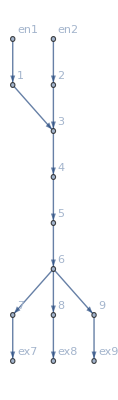

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

```mathematica
oldrules=<|j641->1,j642->2,j643->3,j644->3,j645->3,j646->2,j647->1,j648->0,j649->2,j650->1,j651->0,j652->1,j653->2,j654->0,j655->0,j656->0,j657->0,j658->0,j659->0,j660->0,j661->0,j662->0,j663->0,j664->0,j665->0,j666->0,jt667->0,jt668->1,jt669->0,jt670->2,jt671->0,jt672->1,jt673->0,jt674->2,jt675->0,jt676->0,jt677->3,jt678->0,jt679->3,jt680->0,jt681->2,jt682->1,jt683->0,jt684->0,jt685->0,jt686->0,jt687->0,jt688->0,jt689->0,jt690->0,jt691->0,jt692->0,jt693->2,jt694->0,jt695->1,jt696->0,jt697->0,jt698->0,u699->13,u700->14,u701->12,u702->9,u703->6,u704->3,u705->3,u706->3,u707->1,u708->2,u709->3,u710->13,u711->14,u712->12,u713->12,u714->9,u715->6,u716->3,u717->1,u718->2,u719->3,u720->1,u721->2,u722->3,u723->13,u724->14|>;
```

{<|u1→13,u2→12,u3→14,u4→12,u5→12,u6→9,u7→9,u8→6,u9→6,u10→3,u11→3,u12→1,u13→3,u14→2,u15→3,u16→3,u17→1,u18→1,u19→2,u20→2,u21→3,u22→3,u23→13,u24→13,u25→14,u26→14,j1→0,j2→1,j3→0,j4→2,j5→0,j6→3,j7→0,j8→3,j9→0,j10→3,j11→0,j12→2,j13→0,j14→1,j15→0,j16→0,j17→0,j18→2,j19→0,j20→1,j21→0,j22→0,j23→0,j24→1,j25→0,j26→2|>}

```mathematica
(rul=CriticalCongestionSolver2[MFGEquations];)//AbsoluteTiming
```

EliminateVarsSimplify for the us

Finished with the us!

Finish with the js

{0.068707,Null}

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.77181,j647→0.228186,j648→2.77556×10^-17,j649→2.77181,j650→0.228186,j651→2.77556×10^-17,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.77181,jt682→0.228186,jt683→2.77556×10^-17,jt684→0,jt685→0,jt686→0,jt687→0,jt688→2.77556×10^-17,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.77181,jt694→0,jt695→0.228186,jt696→0,jt697→2.77556×10^-17,jt698→0,u699→9.48121,u700→9.80869,u701→8.22129,u702→6.40417,u703→4.58704,u704→2.76992,u705→2.76992,u706→2.76992,u707→1,u708→2,u709→3,u710→9.48121,u711→9.80869,u712→8.22129,u713→8.22129,u714→6.40417,u715→4.58704,u716→2.76992,u717→1.,u718→2.,u719→2.76992,u720→1,u721→2,u722→3,u723→9.48121,u724→9.80869|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.682,j647→0.317999,j648→1.66533×10^-16,j649→2.682,j650→0.317999,j651→1.66533×10^-16,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.682,jt682→0.317999,jt683→1.66533×10^-16,jt684→0,jt685→0,jt686→0,jt687→0,jt688→1.66533×10^-16,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.682,jt694→0,jt695→0.317999,jt696→0,jt697→1.66533×10^-16,jt698→0,u699→9.68609,u700→10.059,u701→8.44609,u702→6.56504,u703→4.68399,u704→2.80294,u705→2.80294,u706→2.80294,u707→1,u708→2,u709→3,u710→9.68609,u711→10.059,u712→8.44609,u713→8.44609,u714→6.56504,u715→4.68399,u716→2.80294,u717→1.,u718→2.,u719→2.80294,u720→1,u721→2,u722→3,u723→9.68609,u724→10.059|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.49719,j647→0.502811,j648→-2.22045×10^-16,j649→2.49719,j650→0.502811,j651→-2.22045×10^-16,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.49719,jt682→0.502811,jt683→-2.22045×10^-16,jt684→0,jt685→0,jt686→0,jt687→0,jt688→0.,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.49719,jt694→0,jt695→0.502811,jt696→0,jt697→-2.22045×10^-16,jt698→0,u699→10.1503,u700→10.6244,u701→8.9534,u702→6.92212,u703→4.89084,u704→2.85956,u705→2.85956,u706→2.85956,u707→1,u708→2,u709→3,u710→10.1503,u711→10.6244,u712→8.9534,u713→8.9534,u714→6.92212,u715→4.89084,u716→2.85956,u717→1.,u718→2.,u719→2.85956,u720→1,u721→2,u722→3,u723→10.1503,u724→10.6244|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.05436,j647→0.945639,j648→1.11022×10^-16,j649→2.05436,j650→0.945639,j651→1.11022×10^-16,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.05436,jt682→0.945639,jt683→1.11022×10^-16,jt684→0,jt685→0,jt686→0,jt687→0,jt688→1.11022×10^-16,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.05436,jt694→0,jt695→0.945639,jt696→0,jt697→1.11022×10^-16,jt698→0,u699→12.3941,u700→13.2956,u701→11.3605,u702→8.56788,u703→5.77524,u704→2.98259,u705→2.98259,u706→2.98259,u707→1,u708→2,u709→3,u710→12.3941,u711→13.2956,u712→11.3605,u713→11.3605,u714→8.56788,u715→5.77524,u716→2.98259,u717→1.,u718→2.,u719→2.98259,u720→1,u721→2,u722→3,u723→12.3941,u724→13.2956|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j641-j654-u699+u712==0&&j642-j655-u700+u713==0&&j643-j656-u701+u714==0&&j644-j657-u702+u715==0&&j645-j658-u703+u716==0&&j646-j659-u704+u717==0&&j647-j660-u705+u718==0&&j648-j661-u706+u719==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[7.08458×10^-15,ComplexInfinity]

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2,j647→1,j648→0,j649→2,j650→1,j651→0,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2,jt682→1,jt683→0,jt684→0,jt685→0,jt686→0,jt687→0,jt688→0,jt689→0,jt690→0,jt691→0,jt692→0,jt693→2,jt694→0,jt695→1,jt696→0,jt697→0,jt698→0,u699→13,u700→14,u701→12,u702→9,u703→6,u704→3,u705→3,u706→3,u707→1,u708→2,u709→3,u710→13,u711→14,u712→12,u713→12,u714→9,u715→6,u716→3,u717→1,u718→2,u719→3,u720→1,u721→2,u722→3,u723→13,u724→14|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.21537,j647→0.595746,j648→0.188883,j649→2.21537,j650→0.595746,j651→0.188883,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.21537,jt682→0.595746,jt683→0.188883,jt684→0,jt685→0,jt686→0,jt687→0,jt688→1.11022×10^-16,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.21537,jt694→0,jt695→0.595746,jt696→0,jt697→0.188883,jt698→0,u699→23.7948,u700→26.0111,u701→23.1063,u702→16.3633,u703→9.62034,u704→2.87737,u705→2.87737,u706→2.87737,u707→1,u708→2,u709→3,u710→23.7948,u711→26.0111,u712→23.1063,u713→23.1063,u714→16.3633,u715→9.62034,u716→2.87737,u717→1.,u718→2.,u719→3.,u720→1,u721→2,u722→3,u723→23.7948,u724→26.0111|>

```mathematica
alpha = 1.77;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.295,j647→0.389467,j648→0.315537,j649→2.295,j650→0.389467,j651→0.315537,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.295,jt682→0.389467,jt683→0.315537,jt684→0,jt685→0,jt686→0,jt687→0,jt688→5.55112×10^-17,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.295,jt694→0,jt695→0.389467,jt696→0,jt697→0.315537,jt698→0,u699→26.631,u700→29.0696,u701→25.983,u702→18.291,u703→10.5989,u704→2.90684,u705→2.90684,u706→2.90684,u707→1,u708→2,u709→3,u710→26.631,u711→29.0696,u712→25.983,u713→25.983,u714→18.291,u715→10.5989,u716→2.90684,u717→1.,u718→2.,u719→3.,u720→1,u721→2,u722→3,u723→26.631,u724→29.0696|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],4,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.39089,j647→0.190472,j648→0.418639,j649→2.39089,j650→0.190472,j651→0.418639,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.39089,jt682→0.190472,jt683→0.418639,jt684→0,jt685→0,jt686→0,jt687→0,jt688→1.66533×10^-16,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.39089,jt694→0,jt695→0.190472,jt696→0,jt697→0.418639,jt698→0,u699→28.1669,u700→30.7118,u701→27.537,u702→19.3599,u703→11.1829,u704→3.00585,u705→3.00585,u706→3.00585,u707→1,u708→2,u709→3,u710→28.1669,u711→30.7118,u712→27.537,u713→27.537,u714→19.3599,u715→11.1829,u716→3.00585,u717→1.,u718→2.,u719→3.,u720→1,u721→2,u722→3,u723→28.1669,u724→30.7118|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→2.21132,j647→0.271733,j648→0.516942,j649→2.21132,j650→0.271733,j651→0.516942,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→2.21132,jt682→0.271733,jt683→0.516942,jt684→0,jt685→0,jt686→0,jt687→0,jt688→1.11022×10^-16,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→2.21132,jt694→0,jt695→0.271733,jt696→0,jt697→0.516942,jt698→0,u699→34.5883,u700→37.5475,u701→34.0211,u702→23.7512,u703→13.4813,u704→3.21132,u705→3.21132,u706→3.21132,u707→1,u708→2,u709→3,u710→34.5883,u711→37.5475,u712→34.0211,u713→34.0211,u714→23.7512,u715→13.4813,u716→3.21132,u717→1.,u718→2.,u719→3.,u720→1,u721→2,u722→3,u723→34.5883,u724→37.5475|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],9,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

<|j641→1,j642→2,j643→3,j644→3,j645→3,j646→0,j647→1.94947,j648→1.05053,j649→0,j650→1.94947,j651→1.05053,j652→1,j653→2,j654→0,j655→0,j656→0,j657→0,j658→0,j659→0,j660→0,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→1,jt669→0,jt670→2,jt671→0,jt672→1,jt673→0,jt674→2,jt675→0,jt676→0,jt677→3,jt678→0,jt679→3,jt680→0,jt681→0,jt682→1.94947,jt683→1.05053,jt684→0,jt685→0,jt686→0,jt687→0,jt688→0.,jt689→0.,jt690→0,jt691→0.,jt692→0.,jt693→0,jt694→0,jt695→1.94947,jt696→0,jt697→1.05053,jt698→0,u699→44.6378,u700→48.1378,u701→44.1378,u702→30.6378,u703→17.1378,u704→3.63777,u705→3.63777,u706→3.63777,u707→1,u708→2,u709→3,u710→44.6378,u711→48.1378,u712→44.1378,u713→44.1378,u714→30.6378,u715→17.1378,u716→3.63777,u717→0.461549,u718→2.,u719→3.,u720→1,u721→2,u722→3,u723→44.6378,u724→48.1378|>

## format:

```mathematica
(*Wolfram Language package*)ConsistentSwithingCosts::usage="ConsistentSwithingCosts[switching costs][one switching cost]  returns the condition for this switching cost to satisfy the triangle inequality"
ConsistentSwithingCosts[sc_][{a_,b_,c_,S_}]:=Module[{origin,destination,bounds},origin=Cases[sc,{a,b,_,_}];
destination=Cases[sc,{_,b,c,_}];
bounds=Outer[Plus,Last/@origin,Last/@destination]//Flatten;
Print[bounds];
And@@(#>=S&)/@bounds];

IsSwitchingCostConsistent::usage="IsSwitchingCostConsistent[list of switching costs] is True if all switching costs satisfy the triangle inequality"
IsSwitchingCostConsistent[SC_]:=And@@Simplify[ConsistentSwithingCosts[SC]/@SC]

AtHead[DirectedEdge[a_,b_]]:={b,DirectedEdge[a,b]}

AtTail[DirectedEdge[a_,b_]]:={a,DirectedEdge[a,b]}

TransitionsAt[G_,k_]:=Prepend[#,k]&/@Permutations[IncidenceList[G,k],{2}]

RoundValues[x_?NumberQ]:=Round[x,10^-10]

RoundValues[Rule[a_,b_]]:=Rule[a,RoundValues[b]]

RoundValues[x_List]:=RoundValues/@x

RoundValues[x_Association]:=RoundValues/@x

triple2path[{a_,b_,c_},G_]:=Module[{EL=EdgeList[G]},If[SubsetQ[AdjacencyList[G,b],{a,c}],If[MemberQ[EL,DirectedEdge[a,b]],If[MemberQ[EL,DirectedEdge[b,c]],{b,DirectedEdge[a,b],DirectedEdge[b,c]},{b,DirectedEdge[a,b],DirectedEdge[c,b]}],If[MemberQ[EL,DirectedEdge[b,a]],If[MemberQ[EL,DirectedEdge[b,c]],{b,DirectedEdge[b,a],DirectedEdge[b,c]},{b,DirectedEdge[b,a],DirectedEdge[c,b]}]]],StringJoin["\nThere is no path from ",ToString[a]," to ",ToString[b]," to ",ToString[c]]]]

path2triple[{a_,b_->c_,d_->e_}->S_]:={Select[{b,c},#=!=a&],a,Select[{d,e},#=!=a&],S}//Flatten;

CurrentCompCon[jvars_][a_->b_]:=jvars[{a,a->b}]==0||jvars[{b,a->b}]==0;

CurrentSplitting[AllTransitions_][{c_,a_->b_}]:=Select[AllTransitions,(Take[#,2]=={c,a->b})&];

CurrentGathering[AllTransitions_][{c_,a_->b_}]:=Select[AllTransitions,(Part[#,{1,3}]==OtherWay[{c,a->b}])&];

TransitionCompCon[jtvars_][{v_,edge1_,edge2_}]:=jtvars[{v,edge1,edge2}]==0||jtvars[{v,edge2,edge1}]==0;

IncomingEdges[FG_][k_]:={k,#1}&/@IncidenceList[FG,k];

OtherWay[{c_,DirectedEdge[a_,b_]}]:={If[c===a,b,a],DirectedEdge[a,b]}

OutgoingEdges[FG_][k_]:=OtherWay/@({k,#}&/@IncidenceList[FG,k]);

ExitRules[uvars_,ExitCosts_][a_->b_]:=Total[uvars/@{{b,DirectedEdge[a,b]}}]->ExitCosts[b];

ExitCurrents[jvars_][a_->b_]:=jvars@{a,DirectedEdge[a,b]}->0;

Transu[uvars_,SwitchingCosts_][{v_,edge1_,edge2_}]:=uvars[{v,edge1}]<=uvars[{v,edge2}]+SwitchingCosts[{v,edge1,edge2}];

Compu[jtvars_,uvars_,SwitchingCosts_][{v_,edge1_,edge2_}]:=(jtvars[{v,edge1,edge2}]==0)||uvars[{v,edge2}]-uvars[{v,edge1}]+SwitchingCosts[{v,edge1,edge2}]==0;

Data2Equations::usage="Data2Equations[Data] returns the equations, inequalities, and alternatives associated to the Data"
Data2Equations[Data_Association]:=Module[{VL,AM,EVC,EVTC,SC,BG,EntranceVertices,InwardVertices,ExitVertices,OutwardVertices,InEdges,OutEdges,AuxiliaryGraph,FG,EL,BEL,FVL,jargs,uargs,AllTransitions,EntryArgs,EntryDataAssociation,ExitCosts,js,jvars,us,uvars,jts,jtvars,SignedCurrents,SwitchingCosts,EqPosJs,EqPosJts,EqCurrentCompCon,EqTransitionCompCon,NoDeadEnds,EqBalanceSplittingCurrents,BalanceSplittingCurrents,NoDeadStarts,RuleBalanceGatheringCurrents,BalanceGatheringCurrents,EqBalanceGatheringCurrents,EqEntryIn,RuleEntryOut,RuleExitCurrentsIn,RuleExitValues,EqValueAuxiliaryEdges,OutRules,InRules,EqSwitchingByVertex,EqCompCon,Nlhs,ModuleVars,ModuleVarsNames},VL=Lookup[Data,"Vertices List",{}];
AM=Lookup[Data,"Adjacency Matrix",{}];
EVC=Lookup[Data,"Entrance Vertices and Currents",{}];
EVTC=Lookup[Data,"Exit Vertices and Terminal Costs",{}];
SC=Lookup[Data,"Switching Costs",{}];
(****Graph stuff****)BG=AdjacencyGraph[VL,AM,VertexLabels->"Name",DirectedEdges->True];
EntranceVertices=First/@EVC;
ExitVertices=First/@EVTC;
Clear["en*","ex*"];
(*InwardVertices defines auxiliary vertices for the entrance vertices*)InwardVertices=AssociationThread[EntranceVertices,Symbol["en"<>ToString[#]]&/@EntranceVertices];
OutwardVertices=AssociationThread[ExitVertices,Symbol["ex"<>ToString[#]]&/@ExitVertices];
(*InEdges defines auxiliary arguments for the entrance vertices*)InEdges=MapThread[DirectedEdge,{InwardVertices/@EntranceVertices,EntranceVertices}];
OutEdges=MapThread[DirectedEdge,{ExitVertices,OutwardVertices/@ExitVertices}];
AuxiliaryGraph=Graph[Join[InEdges,OutEdges],VertexLabels->"Name",GraphLayout->"SpringEmbedding"];
FG=EdgeAdd[BG,Join[InEdges,OutEdges]];
EL=EdgeList[FG];
BEL=EdgeList[BG];
FVL=VertexList[FG];
(*arguments*)jargs=Flatten[#,1]&@({AtTail@#,AtHead@#}&/@EL);
uargs=jargs;
(*AllTransitions=TransitionsAt[BG,#]&/@VL//Catenate(*at vertex from first edge to second edge*);*)AllTransitions=TransitionsAt[FG,#]&/@FVL//Catenate(*at vertex from first edge to second edge*);
EntryArgs=AtHead/@((EdgeList[AuxiliaryGraph,DirectedEdge[_,#]]&/@(First/@EVC))//Flatten[#,1]&);
EntryDataAssociation=RoundValues@AssociationThread[EntryArgs,Last/@EVC];
ExitCosts=AssociationThread[OutwardVertices/@(First/@EVTC),Last/@EVTC];
(*variables*)js=Table[Symbol["j"<>ToString[k]],{k,1,Length@jargs}];
jvars=AssociationThread[jargs,js];
jts=Table[Symbol["jt"<>ToString[k]],{k,1,Length@AllTransitions}];
jtvars=AssociationThread[AllTransitions,jts];
us=Table[Symbol["u"<>ToString[k]],{k,1,Length@uargs}];
uvars=AssociationThread[uargs,us];
SignedCurrents=AssociationThread[BEL,(jvars[AtHead[#]]-jvars[AtTail[#]]&)/@BEL];
(*Print["D2E: Variables are all set"];*)(*Elements of the system*)(*Swithing cost is initialized with 0. AssociationThread associates the last association!*)(*SwitchingCosts=AssociationThread[Join[AllTransitions,triple2path[Take[#,3],BG]&/@SC],Join[0&/@AllTransitions,Last[#]&/@SC]];*)SwitchingCosts=AssociationThread[Join[AllTransitions,triple2path[Take[#,3],FG]&/@SC],Join[0&/@AllTransitions,Last[#]&/@SC]];
EqPosJs=And@@(#>=0&/@Join[jvars]);(*Inequality*)EqPosJts=And@@(#>=0&/@Join[jtvars]);(*Inequality*)EqCurrentCompCon=And@@(CurrentCompCon[jvars]/@EL);(*Or*)EqTransitionCompCon=And@@((Sort/@TransitionCompCon[jtvars]/@AllTransitions)//Union);(*Or*)(*Balance Splitting Currents in the full graph*)(*NoDeadEnds=IncomingEdges[BG]/@VL//Flatten[#,1]&;*)NoDeadEnds=IncomingEdges[FG]/@VL//Flatten[#,1]&;
BalanceSplittingCurrents=((jvars[#]-Total[jtvars/@CurrentSplitting[AllTransitions][#]])&/@NoDeadEnds);
EqBalanceSplittingCurrents=Simplify/@(And@@((#==0)&/@BalanceSplittingCurrents));(*Equal*)(*Gathering currents in the inside of the basic graph*)(*NoDeadStarts=OutgoingEdges[BG]/@VL//Flatten[#,1]&;*)NoDeadStarts=OutgoingEdges[FG]/@VL//Flatten[#,1]&;
RuleBalanceGatheringCurrents=Association[(jvars[#]->Total[jtvars/@CurrentGathering[AllTransitions][#]])&/@NoDeadStarts];(*Rule*)(*get equations for the exit currents at the entry vertices*)BalanceGatheringCurrents=((-jvars[#]+Total[jtvars/@CurrentGathering[AllTransitions][#]])&/@NoDeadStarts);
EqBalanceGatheringCurrents=Simplify/@(And@@(#==0&/@BalanceGatheringCurrents));
(*Incoming currents*)EqEntryIn=(jvars[#]==EntryDataAssociation[#])&/@(AtHead/@InEdges);(*List of Equals*)(*Outgoing currents at entrances*)RuleEntryOut=Association[(jvars[#]->0)&/@(AtTail/@InEdges)];(*Rule*)RuleExitCurrentsIn=Association[ExitCurrents[jvars]/@OutEdges];(*Rule*)(*Exit values at exit vertices*)RuleExitValues=Association[ExitRules[uvars,ExitCosts]/@OutEdges];(*Rule*)(*The value function on the auxiliary edges is constant and equal to the exit cost.*)EqValueAuxiliaryEdges=And@@((uvars[AtTail[#]]==uvars[AtHead[#]])&/@Join[InEdges,OutEdges]);(*Equal*)(*use ToRules to get the rules*)OutRules=Rule[#,Infinity]&/@(Outer[Flatten[{AtTail[#1],#2}]&,OutEdges,EL]//Flatten[#,1]&);
InRules=Rule[#,Infinity]&/@(Outer[{#2[[2]],#1,#2}&,IncidenceList[FG,#]&/@EntranceVertices,InEdges]//Flatten[#,2]&);
(*Switching condition equations*)(*EqSwitchingByVertex=Transu[uvars,SwitchingCosts]/@TransitionsAt[BG,#]&/@VL;*)EqSwitchingByVertex=Transu[uvars,SwitchingCosts]/@TransitionsAt[FG,#]&/@VL;
EqSwitchingByVertex=(And@@#)&/@EqSwitchingByVertex;
EqCompCon=And@@Compu[jtvars,uvars,SwitchingCosts]/@AllTransitions;(*Or*)Nlhs=Flatten[uvars[AtHead[#]]-uvars[AtTail[#]]+SignedCurrents[#]&/@BEL];
ModuleVars=(*list of all module variables,except for ModuleVars*){VL,AM,EVC,EVTC,SC,BG,EntranceVertices,InwardVertices,ExitVertices,OutwardVertices,InEdges,OutEdges,AuxiliaryGraph,FG,EL,BEL,FVL,jargs,uargs,AllTransitions,EntryArgs,EntryDataAssociation,ExitCosts,js,jvars,us,uvars,jts,jtvars,SignedCurrents,SwitchingCosts,EqPosJs,EqPosJts,EqCurrentCompCon,EqTransitionCompCon,NoDeadEnds,EqBalanceSplittingCurrents,BalanceSplittingCurrents,NoDeadStarts,RuleBalanceGatheringCurrents,BalanceGatheringCurrents,EqBalanceGatheringCurrents,EqEntryIn,RuleEntryOut,RuleExitCurrentsIn,RuleExitValues,EqValueAuxiliaryEdges,OutRules,InRules,EqSwitchingByVertex,EqCompCon,Nlhs};
ModuleVarsNames={"VL","AM","EVC","EVTC","SC","BG","EntranceVertices","InwardVertices","ExitVertices","OutwardVertices","InEdges","OutEdges","AuxiliaryGraph","FG","EL","BEL","FVL","jargs","uargs","AllTransitions","EntryArgs","EntryDataAssociation","ExitCosts","js","jvars","us","uvars","jts","jtvars","SignedCurrents","SwitchingCosts","EqPosJs","EqPosJts","EqCurrentCompCon","EqTransitionCompCon","NoDeadEnds","EqBalanceSplittingCurrents","BalanceSplittingCurrents","NoDeadStarts","RuleBalanceGatheringCurrents","BalanceGatheringCurrents","EqBalanceGatheringCurrents","EqEntryIn","RuleEntryOut","RuleExitCurrentsIn","RuleExitValues","EqValueAuxiliaryEdges","OutRules","InRules","EqSwitchingByVertex","EqCompCon","Nlhs"};
Join[Data,AssociationThread[ModuleVarsNames,ModuleVars]]];

GetKirchhoffMatrix[Eqs_]:=Module[{Kirchhoff,EqEntryIn=Lookup[Eqs,"EqEntryIn",True],BalanceGatheringCurrents=Lookup[Eqs,"BalanceGatheringCurrents",{}],BalanceSplittingCurrents=Lookup[Eqs,"BalanceSplittingCurrents",{}],RuleExitCurrentsIn=Lookup[Eqs,"RuleExitCurrentsIn",{}],RuleEntryOut=Lookup[Eqs,"RuleEntryOut",{}],BM,KM,vars},Kirchhoff=Join[EqEntryIn,(#==0&/@(BalanceGatheringCurrents+BalanceSplittingCurrents))];
Kirchhoff=Kirchhoff/. Join[RuleExitCurrentsIn,RuleEntryOut];
{BM,KM}=CoefficientArrays[Kirchhoff,vars=Variables[Kirchhoff/. Equal->Plus]];
Print["The matrices B and K are: \n",MatrixForm/@{-BM,KM},"\nThe order of the variables is \n",vars];
{-BM,KM,vars}];

MFGPreprocessing[Eqs_]:=Module[{InitRules,RuleBalanceGatheringCurrents,EqEntryIn,RuleEntryOut,RuleExitCurrentsIn,RuleExitValues,EqValueAuxiliaryEdges,EqSwitchingByVertex,EqCompCon,EqBalanceSplittingCurrents,EqCurrentCompCon,EqTransitionCompCon,EqPosJs,EqPosJts,ModuleVarsNames,ModulesVars,NewSystem},RuleBalanceGatheringCurrents=Lookup[Eqs,"RuleBalanceGatheringCurrents",$Failed];
EqEntryIn=Lookup[Eqs,"EqEntryIn",$Failed];
RuleEntryOut=Lookup[Eqs,"RuleEntryOut",$Failed];
RuleExitCurrentsIn=Lookup[Eqs,"RuleExitCurrentsIn",$Failed];
RuleExitValues=Lookup[Eqs,"RuleExitValues",$Failed];
EqValueAuxiliaryEdges=Lookup[Eqs,"EqValueAuxiliaryEdges",$Failed];
EqSwitchingByVertex=Lookup[Eqs,"EqSwitchingByVertex",$Failed];
EqCompCon=Lookup[Eqs,"EqCompCon",$Failed];
EqBalanceSplittingCurrents=Lookup[Eqs,"EqBalanceSplittingCurrents",$Failed];
EqCurrentCompCon=Lookup[Eqs,"EqCurrentCompCon",$Failed];
EqTransitionCompCon=Lookup[Eqs,"EqTransitionCompCon",$Failed];
EqPosJs=Lookup[Eqs,"EqPosJs",$Failed];
EqPosJts=Lookup[Eqs,"EqPosJts",$Failed];
(*TODO Check switching costs for consistency*)(*First rules:entry currents*)InitRules=Association[Flatten[ToRules/@EqEntryIn]];
(*no exit at the entrances*)AssociateTo[InitRules,RuleEntryOut];
(*no entrance at the exits*)AssociateTo[InitRules,RuleExitCurrentsIn];
(*currents gathered from transition currents*)AssociateTo[InitRules,RuleBalanceGatheringCurrents];
(*value function:exit costs*)AssociateTo[InitRules,RuleExitValues];
EqSwitchingByVertex=And@@(Simplify/@(EqSwitchingByVertex/. InitRules));
(*Print[1];
Print[Sys2Triple[EqSwitchingByVertex]];*)NewSystem=MapThread[And,{{EqBalanceSplittingCurrents&&EqValueAuxiliaryEdges,EqPosJts&&EqPosJs,EqCurrentCompCon&&EqTransitionCompCon&&EqCompCon},Sys2Triple[EqSwitchingByVertex]}];
(*Print[NewSystem];*){NewSystem,InitRules}=TripleClean[{NewSystem,InitRules}];
Print["tripleclean done!"];
(*return something!!!*)ModuleVarsNames={"InitRules","RuleBalanceGatheringCurrents","EqEntryIn","RuleEntryOut","RuleExitCurrentsIn","RuleExitValues","EqValueAuxiliaryEdges","EqSwitchingByVertex","EqCompCon","EqBalanceSplittingCurrents","EqCurrentCompCon","EqTransitionCompCon","EqPosJs","EqPosJts","NewSystem"};
ModulesVars={InitRules,RuleBalanceGatheringCurrents,EqEntryIn,RuleEntryOut,RuleExitCurrentsIn,RuleExitValues,EqValueAuxiliaryEdges,EqSwitchingByVertex,EqCompCon,EqBalanceSplittingCurrents,EqCurrentCompCon,EqTransitionCompCon,EqPosJs,EqPosJts,NewSystem}/. InitRules;
Join[Eqs,AssociationThread[ModuleVarsNames,ModulesVars]]];

CriticalCongestionSolver[Eqs_]:=Module[{PreEqs,Nlhs,EqCritical,InitRules,NewSystem},PreEqs=MFGPreprocessing[Eqs];
Print["Preprocessing done!"];
Nlhs=Lookup[PreEqs,"Nlhs",$Failed];
InitRules=Lookup[PreEqs,"InitRules",$Failed];
NewSystem=Lookup[PreEqs,"NewSystem",$Failed];
(*Updated (with rules from preprocessing) edge equations*)EqCritical=(And@@((#==0)&/@Nlhs))/.InitRules;
(*Print["22: ",EqCritical];*){NewSystem,InitRules}=TripleClean[{Join[{EqCritical},Take[NewSystem,{2,3}]],InitRules}];
(*Print["33: ",NewSystem];*)NewSystem=NewReduce[And@@NewSystem];
NewSystem=BooleanConvert[NewSystem,"CNF"];
(*Print["44: ",NewSystem];*)NewSystem=Sys2Triple[BooleanConvert[Reduce[NewSystem,Reals],"CNF"]];
{NewSystem,InitRules}=TripleClean[{NewSystem,InitRules}];
If[And@@NewSystem===False,Print["There is no solution"]];
InitRules];

Sys2Triple[True]=Table[True,3]

Sys2Triple[False]=Table[False,3]

Sys2Triple[system_]:=Which[Head[system]===And,Module[{groups,EE,OR,NN},groups=GroupBy[List@@system,Head[#]===Equal&];
EE=And@@Lookup[groups,True,{}];
groups=GroupBy[Lookup[groups,False,{}],Head[#]===Or&];
OR=And@@Lookup[groups,True,True];
NN=And@@Lookup[groups,False,True];
{EE,NN,OR}],Head[system]===Equal,{system,True,True},Head[system]===Or,{True,True,system},True,{True,system,True}];

TripleStep[{{EEs_,NNs_,ORs_},rules_List}]:=TripleStep[{{EEs,NNs,ORs},Association@rules}]

TripleStep[{{EE_?TrueQ,NN_?TrueQ,OR_?TrueQ},rules_}]:={Table[True,3],rules}

TripleStep[{{EE_,NN_?TrueQ,OR_?TrueQ},rules_Association}]:=Module[{newrules={}},newrules=First@Solve[EE]//Quiet;
newrules=Join[rules/. newrules,Association@newrules];
{{True,NN,OR},Expand/@newrules}];

TripleStep[{{EEs_,NNs_,ORs_},rules_Association}]:=Module[{EE=EEs/. rules,NN=NNs/. rules,OR=ORs/. rules,NNE,NNO,ORE,ORN,bool,newrules={}},bool=EE&&NN&&OR;
If[BooleanQ[bool],Return[{Table[bool,3],rules},Module]];
(*Print["nn: ",NN];*)NN=Simplify[NN];
(*Print["nn: ",NN];*){NNE,NN,NNO}=Sys2Triple[NN];
(*Print["nn: ",NN];*)(*Print["or: ",OR];*){ORE,ORN,OR}=Sys2Triple[OR];
EE=EE&&NNE&&ORE;
(*Print["56: ",EE];*)If[EE=!=True&&EE=!=False,newrules=First@Solve[EE]//Quiet];
newrules=Join[rules/. newrules,Association@newrules];
(*Print[{{EE,NN,OR},Expand/@newrules}];*){{EE,NN,OR},Expand/@newrules}];

TripleClean[{{EE_,NN_,OR_},rules_}]:=FixedPoint[TripleStep,{{EE,NN,OR},rules}]


(*TODO review NewReduce and maybe make it take triple-systems*)
NewReduce[s_Or]:=Reduce[s,Reals]

NewReduce[True]:=True

NewReduce[False]:=False

NewReduce[x_Equal]:=(Print["here"];
Reduce[x,Reals])

NewReduce[s_Inequality]:=s

NewReduce[x_GreaterEqual]:=x

NewReduce[x_LessEqual]:=x

NewReduce[x_Inequality]:=x

(*TODO NewReduce:is there a problem here?*)
NewReduce[system_And]:=Module[{result,groups=GroupBy[List@@system,Head[#]===Or||Head[#]===Equal&],subgroups,sorted},subgroups=GroupBy[groups[True],Head[#]===Equal&];
If[Head[subgroups[False]]===Missing,result=ZAnd[And@@Lookup[groups,False,True],And@@Lookup[subgroups,True,True]],sorted=SortBy[And@@Lookup[subgroups,False,True],Simplify`SimplifyCount];
result=ZAnd[And@@Lookup[groups,False,True],(And@@Lookup[subgroups,True,True])&&sorted]];
(*result=ZAnd[Select[system,!((Head[#]===Or)||(Head[#]===Equal))&],Select[system,((Head[#]===Or)||(Head[#]===Equal))&]];*)If[result=!=False,result=result//DeleteDuplicates];
result]

ZAnd[_,False]:=(False)

ZAnd[xp_,leq_LessEqual]:=Simplify[xp&&leq]

ZAnd[xp_,geq_GreaterEqual]:=Simplify[xp&&geq]

ZAnd[xp_,ineq_Inequality]:=Simplify[xp&&ineq]

ZAnd[False,_]:=(False)

ZAnd[xp_,True]:=xp

ZAnd[xp_,eq_Equal]:=With[{sol=Solve[eq]},If[sol==={},False,(xp/. First[sol])&&And@@(First[sol]/. Rule->Equal)//Simplify]]

ZAnd[xp_,orxp_Or]:=(Print["Do we need removeduplicates?\n",(ZAnd[xp,#]&/@orxp)];
(ZAnd[xp,#]&/@orxp) (*//RemoveDuplicates*))

ZAnd[xp_,andxp_And]:=With[{fst=First[andxp],rst=Rest[andxp]},Which[Head[fst]===Or,ReZAnd[xp,rst]/@fst (*//RemoveDuplicates*),Head[fst]===And,ReZAnd[xp,rst,fst],True,ReZAnd[xp,rst,fst]]]

(*Operator form of ReZAnd*)
ReZAnd[xp_,rst_]:=ReZAnd[xp,rst,#]&

ReZAnd[xp_,rst_,fst_Equal]:=Module[{fsol=First@Solve@fst//Quiet},ZAnd[(xp/. fsol)&&And@@(fsol/. Rule->Equal)//Simplify,ReplaceSolution[rst,fsol]]]

ReZAnd[xp_,rst_,fst_And]:=ReZAnd[xp,rst]/@fst

ReZAnd[xp_,rst_,fst_(*Inequality]:=ZAnd[xp&&fst,rst] ReZAnd[xp_,rst_,fst_LessEqual]:=ZAnd[xp&&fst,rst] ReZAnd[xp_,rst_,fst_GreaterEqual]:=ZAnd[xp&&fst,rst] ReZAnd[xp_,rst_,fst_Less]:=ZAnd[xp&&fst,rst] ReZAnd[xp_,rst_,fst_Greater*)]:=ZAnd[xp&&fst,rst]

ReplaceSolution[rst_?BooleanQ,sol_]:=rst

(*ReplaceSolution[False,sol_]:=False*)

ReplaceSolution[rst_,sol_]:=Module[{newrst},newrst=rst/. sol;
If[Head[newrst]===And,Reduce[#,Reals]&/@newrst,Reduce[newrst,Reals]]]

(*ReplaceSolution[rst_,sol_]:=Simplify[rst/. sol]*)

(*RemoveDuplicates[xp_And]:=DeleteDuplicates[Sort[xp]];
RemoveDuplicates[xp_Or]:=DeleteDuplicates[Sort[xp]];
RemoveDuplicates[xp_]:=xp*)
```